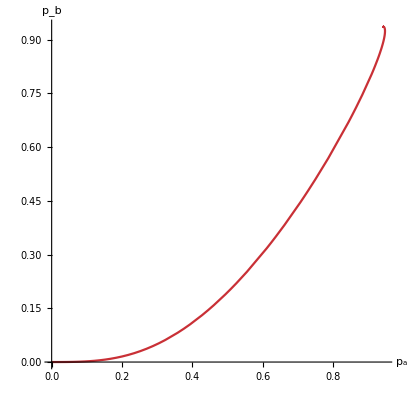

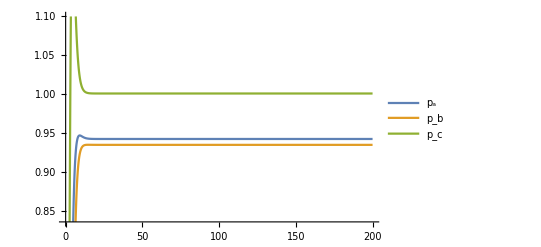

```mathematica
SuperPlus[h][p_, θ_, n_] := p^n/(p^n + θ^n)
SuperMinus[h][p_, θ_, n_] := 1-SuperPlus[h][p, θ, n]

tmax=200;

With[{ma=1., mb=1.,mc=1.,
	na=2.2, nb=2.2,nc=2.2,
	θa=0.28, θb=0.28,θc=0.28,
	 ka=1., kb=1., kc = 1.,
	γa=1., γb=1., γc=1.,
	δa=1., δb=1., δc=1.},
		sol=NDSolve[{Subscript[r, a]'[t] == ma*(SuperPlus[h][Subscript[p, c][t], θc, nc])-γa*Subscript[r, a][t],
					Subscript[r, b]'[t] == mb*(SuperPlus[h][Subscript[p, a][t], θa, na])-γb*Subscript[r, b][t],
					Subscript[r, c]'[t] == mc*(SuperMinus[h][Subscript[p, b][t], θb, nb]+SuperPlus[h][Subscript[p, a][t], θa, na])-γc*Subscript[r, c][t],
					Subscript[p, a]'[t] == ka*Subscript[r, a][t]-δa*Subscript[p, a][t],
					Subscript[p, b]'[t] == kb*Subscript[r, b][t]-δb*Subscript[p, b][t],
					Subscript[p, c]'[t] == kc*Subscript[r, c][t]-δc*Subscript[p, c][t],
					Subscript[r, a][0]==0,Subscript[r, b][0]==0,Subscript[r, c][0]==0, Subscript[p, a][0]==0, Subscript[p, b][0]==0, Subscript[p, c][0]==0},
					{Subscript[r, a],Subscript[r, b], Subscript[r, c],Subscript[p, a], Subscript[p, b], Subscript[p, c]},{t, 0, tmax}]];



ParametricPlot[Evaluate[{Subscript[p, a][t],Subscript[p, b][t]}/.First[sol]],{t,0,tmax}, AxesLabel->{Subscript[p, a],Subscript[p, b]},ColorFunction->"Rainbow", PlotRange->Full]

Plot[Evaluate[{Subscript[p, a][t],Subscript[p, b][t], Subscript[p, c][t]}/.First[sol]],{t,0,tmax}, PlotLegends->{"p_a", "p_b", "p_c"}]
```